## Fourier Analysis: Square Wave

```mathematica
$r = 500/800; $onTime=10;
```

```mathematica
F[t_,r_, onTime_]:=1-UnitStep[Mod[t,onTime/r]-onTime]
```

```mathematica
Manipulate[Plot[F[t,r,100],{t,0,400},PlotRange->{0,1.2},Exclusions->None], {{r, 0.5}, 0.01, 0.99}]
```

```mathematica
(*General Functions*)
a[m_, f_, T_]:=2/T ∫_0^T f Cos[(2π m)/T t] ⅆt
b[m_, f_, T_]:=2/T ∫_0^T f Sin[(2π m)/T t] ⅆt
d[m_, f_, T_]:=√(a[m, f, T]^2+b[m, f, T]^2)  ;
φ[m_, f_, T_]:=ArcTan[b[m, f, T],a[m, f, T]];
```

```mathematica
(*For the square wave F*)
Subscript[Sa, m_] := a[m, F[t, $r, $onTime],$onTime/ $r];
Subscript[Sb, m_] := b[m, F[t, $r, $onTime],$onTime/ $r ];
Subscript[Sd, m_]:=d[m, F[t, $r, $onTime],$onTime/ $r ];
Subscript[Sφ, m_]:=φ[m, F[t, $r, $onTime],$onTime/ $r ];
```

```mathematica
Manipulate[DiscretePlot[{
a[m, F[t, r, 1], 10/ r],
b[m, F[t, r, 1], 10/ r]},
{m,0,9},
PlotLabels->{"a_m", "b_m"}, 
PlotRange->Full], {r, 0.1, 0.9}]
```

## Reproducing the signal

```mathematica
Subscript[f, N_][t_] :=1/2 Subscript[Sa, 0] +∑_(m=1)^N (Subscript[Sa, m] Cos[(2π m t)/($onTime/ $r)]+ Subscript[Sb, m] Sin[(2π m t)/($onTime/ $r)]);
```

```mathematica
(*Subscript[f, N_][t_] := 1/2 Subscript[Sa, 0] +∑_(m=1)^N Subscript[Sd, m] Sin[(2π m t)/($onTime/ $r)+Subscript[Sφ, m]]*)
```

```mathematica
$R[N_, t_] = Subscript[f, N][t];
$R[3, t]
```

5/8+1/(2 π)ⅈ ⅇ^(-1/8 ⅈ π t) (1+1/2 ⅇ^(-1/8 ⅈ π t)+1/3 ⅇ^(-1/4 ⅈ π t)-1/6 (-1)^(1/4) ⅇ^(-1/4 ⅈ π t) (-2 ⅈ+3 (-1)^(1/4) ⅇ^((ⅈ π t)/8)-6 ⅇ^((ⅈ π t)/4))+1/6 (-1)^(1/4) ⅇ^((ⅈ π t)/4) (6 ⅈ-3 (-1)^(1/4) ⅇ^((ⅈ π t)/8)+2 ⅇ^((ⅈ π t)/4))+ⅇ^((ⅈ π t)/8) Log[1-ⅇ^(-1/8 ⅈ π t)]+ⅇ^((ⅈ π t)/8) Log[1-ⅇ^((ⅈ π t)/8)]+ⅇ^((ⅈ π t)/4) (-1-1/2 ⅇ^((ⅈ π t)/8)-1/3 ⅇ^((ⅈ π t)/4)-ⅇ^(-1/8 ⅈ π t) Log[1-ⅇ^((ⅈ π t)/8)])-ⅇ^((ⅈ π t)/8) Log[ⅇ^(-1/8 ⅈ π t) (-1+ⅇ^((ⅈ π t)/8))])

```mathematica
(*Subscript[f, N_][t_] := 1/2 Subscript[Sa, 0] +∑_(m=1)^N Subscript[Sd, m] Sin[(2π m t)/($onTime/ $r)+Subscript[Sφ, m]]*)
Plot[{$R[20, t],F[t,$r, $onTime]}, {t, 0, $onTime/ $r},
PlotLabels->"Expressions", Exclusions->None, PlotTheme->"Monochrome"
]
```

$Aborted

```mathematica
{Subscript[f, 5][t]}
```

{5/8-Cos[(π t)/8]/(√2 π)+Cos[(π t)/4]/(2 π)-Cos[(3 π t)/8]/(3 √2 π)+Cos[(5 π t)/8]/(5 √2 π)+((2+√2) Sin[(π t)/8])/(2 π)+Sin[(π t)/4]/(2 π)-((-2+√2) Sin[(3 π t)/8])/(6 π)+Sin[(π t)/2]/(2 π)-((-2+√2) Sin[(5 π t)/8])/(10 π)}

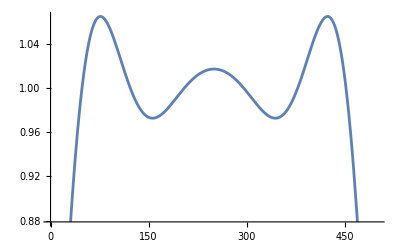

```mathematica
Plot[%380,{t,0,500}]
```

```mathematica
Subscript[Sa, 0]
```

5/4

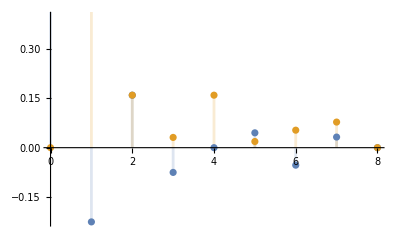

```mathematica
DiscretePlot[{Subscript[Sa, m], Subscript[Sb, m]},{m,0,8}]
```

```mathematica
2/T Integrate[Sin[(2 π m)/T t], {t, 0, T}, Assumptions->{m∈PositiveIntegers}]
```

(2 Sin[m π]^2)/(m π)